Laser Pulse Temporal Envelopes

Notebook: Óscar Amaro, October 2021 @ GoLP-EPP
Contact: oscar.amaro@tecnico.ulisboa.pt

Introduction
PIC codes like OSIRIS allow different models for the temporal profile of a laser pulse, namely sin(t)^2, polynomial and Gaussian. There is usually much confusion on what definition of FWHM to use (whether it is for the field or for intensity). In this notebook we derive these quantities in a systematic way, such that it becomes easy to convert from one form to the other.

Also for reference:
x[c/ωp] = x/(c/ωp) μm/μm = 2π  x[μm]/λ[μm]
t[1/ωp] = t/(1/ωp) fs/fs = t[fs] ωp[1/fs]
Δt[1/ωp] = Δx[c/ωp]
ωp[1/fs] ~ 1.884/λ[μm]

```mathematica
Clear[Esin2,fwhmEsin2,fwhmIsin2,Egauss,Epoly]
```

## Profile Sin2

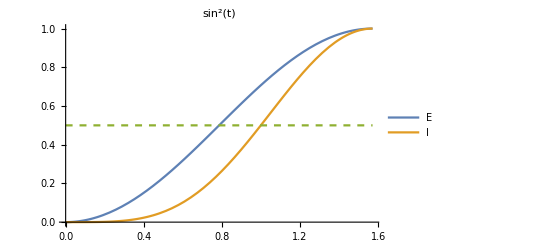

1.5708

1.14372

0.728113

```mathematica
Esin2=Sin[t]^2;

(*fwhm for field is π/2 *)
Plot[{Esin2,Esin2^2,0.5},{t,0,π/2},PlotStyle->{Default,Default,Dashed},PlotLegends->{"E","I"},PlotLabel->Esin2]

fwhmEsin2=π/2//N
(* (sin(x)^2)^2=0.5 -> x=arcsin( (0.5)^0.25 ) *)
x12=NSolve[Esin2^2 ==0.5,t][[4,1,2]]//Quiet;
π-2x12;
fwhmIsin2=π-2ArcSin[(0.5)^0.25]

fwhmIsin2/fwhmEsin2
```

## Profile Polynomial

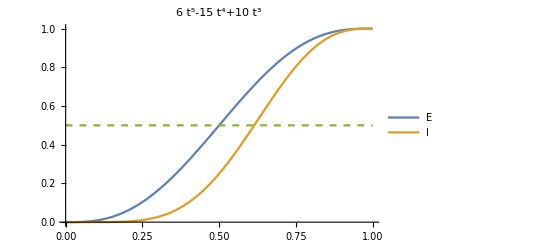

1

0.771229

0.771229

```mathematica
Epoly=10t^3 -15t^4+6 t^5;
Plot[{Epoly,Epoly^2,0.5},{t,0,1},PlotStyle->{Default,Default,Dashed},PlotLegends->{"E","I"},PlotLabel->Epoly]

fwhmEpoly=1
x12=NSolve[Efld^2 ==0.5,t,Reals][[2,1,2]];
fwhmIpoly=2(1-x12)

fwhmIpoly/fwhmEpoly
```

## Profile Gaussian

ⅇ^(-t^2)

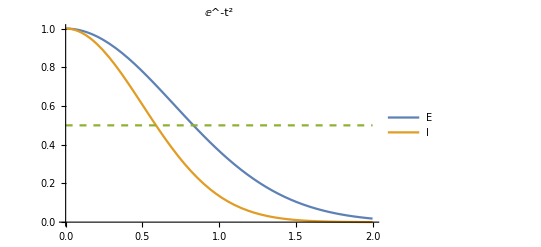

1.66511

1.17741

0.707107

```mathematica
Egauss=Exp[-t^2]
Plot[{Egauss,Egauss^2,0.5},{t,0,2},PlotStyle->{Default,Default,Dashed},PlotLegends->{"E","I"},PlotLabel->Egauss]

fwhmEgauss=2NSolve[Egauss==0.5,t,Reals][[2,1,2]]
fwhmIgauss=2NSolve[Egauss^2==0.5,t,Reals][[2,1,2]]

fwhmIgauss/fwhmEgauss (*Sqrt[2]*)
```

## Results (normalized to some characteristic time τ)

```mathematica
TableForm[{{"","tmax","FWHM E","FWHM I","FWHM I/FWHM E"},{"sin^2",π,fwhmEsin2,fwhmIsin2,fwhmIsin2/fwhmEsin2},{"poly",2,fwhmEpoly,fwhmIpoly,fwhmIpoly/fwhmEpoly},{"gauss",∞,fwhmEgauss,fwhmIgauss,fwhmIgauss/fwhmEgauss}}]
```

| tmax | FWHM E | FWHM I | FWHM I/FWHM E
sin^2 | π | 1.5708 | 1.14372 | 0.728113
poly | 2 | 1 | 0.771229 | 0.771229
gauss | ∞ | 1.66511 | 1.17741 | 0.707107